### Start choosing the example:

```mathematica
t="Jamaratv9";
beta =0;
A = 0.2;
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"];
g[x];
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t];
```

```mathematica
Data
```

<|Vertices List→{1,2,3,4,5,6,7,8,9},Adjacency Matrix→{{0,1,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0},{0,0,0,1,1,0,0,0,0},{0,0,0,0,0,1,0,0,0},{0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,I1},{2,I2}},Exit Vertices and Terminal Costs→{{7,U1},{8,U2},{9,U3}},Switching Costs→{}|>

### Look at the output bellow before trying to rerun!

```mathematica
(*With U2->2, agents don't exit through 6. running with U2->U2 to determine the largest value for which we get some current, hence unicity.*)
```

```mathematica
(rule=CriticalCongestionSolver2[d2e=D2E[Data/.{I1-> 130,I2->(*129*)20, U1-> 20,U2->100,U3->0}]])//AbsoluteTiming(*does not get all us in the first "step"*)
```

Variables are all set

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CleanEqualities for the (non) critical case equations

EliminateVarsSimplify for the us

Not finished with the us!

EliminateVarsSimplify for the js

True

Reducing further (NewReduce)...

Simplifying...

Done!

{29.4118,<|u1→1990/7,u2→245,u3→1990/7,u4→1355/7,u5→245,u6→1300/7,u7→1355/7,u8→1300/7,u9→1355/7,u10→775/7,u11→1300/7,u12→830/7,u13→775/7,u14→830/7,u15→775/7,u16→20,u17→830/7,u18→415/7,u19→20,u20→0,u21→20,u22→20,u23→415/7,u24→0,u25→100,u26→100,u27→0,u28→0,u29→1990/7,u30→1990/7,u31→245,u32→245,j1→0,j2→275/7,j3→0,j4→635/7,j5→0,j6→415/7,j7→0,j8→55/7,j9→0,j10→580/7,j11→0,j12→470/7,j13→55/7,j14→0,j15→0,j16→635/7,j17→0,j18→415/7,j19→0,j20→20,j21→0,j22→495/7,j23→0,j24→415/7,j25→0,j26→0,j27→0,j28→555/7,j29→0,j30→130,j31→0,j32→20|>}

```mathematica
d2e["EqNonCritical"]//Solve
```

{{j24→-cpc10+cpc11+cpc7-cpc8+cpc9+j13-j14-j15+j16+j17-j18-j19+j20+j23,j8→-cpc1+cpc2-cpc3+cpc4-j1+j2+j3-j4-j5+j6+j7,j9→cpc1-cpc2+cpc3-cpc5+cpc6-cpc7+j1+j10+j11-j12-j13+j14-j2-j3+j4+j5-j6,u10→cpc1+cpc3+cpc6-cpc7+j1+j11-j12-j13+j14-j2+j5-j6+u1,u11→cpc1+cpc3+j1-j2+j5-j6+u1,u12→cpc1+cpc3+cpc6+j1+j11-j12-j2+j5-j6+u1,u16→cpc1+cpc3+cpc6-cpc7+cpc8+j1+j11-j12-j13+j14+j15-j16-j2+j5-j6+u1,u18→cpc1+cpc3+cpc6+cpc9+j1+j11-j12+j17-j18-j2+j5-j6+u1,u2→cpc1+j1-j2+u1,u20→cpc1+cpc10+cpc3+cpc6-cpc7+cpc8+j1+j11-j12-j13+j14+j15-j16+j19-j2-j20+j5-j6+u1,u4→cpc2+j3-j4+u1}}

```mathematica
d2e["RuleNonCritical"]
```

<|j2→-jt12+jt19+jt20,j4→jt13+jt14,j29→0,j1→499-cpc1/4+cpc2/4-cpc3/4+cpc4/4-jt12+jt14/4+jt16/4-jt17/4-jt18/4+jt19+jt20,j6→jt19+jt20,j31→0,j3→-501+cpc1/4-cpc2/4+cpc3/4-cpc4/4+jt13+(3 jt14)/4-jt16/4+jt17/4+jt18/4,j8→jt13+jt18,j10→jt14+jt16,j5→-1501-cpc1/4+cpc2/4-cpc3/4+cpc4/4+jt14/4+jt16/4-jt17/4-jt18/4+jt19+jt20,j7→-501+cpc1/4-cpc2/4+cpc3/4-cpc4/4+jt13+(3 jt14)/4+(3 jt16)/4-(3 jt17)/4+jt18/4,j12→jt20+jt22,j9→jt17+jt18,j14→2503-cpc1/4+cpc2/4-cpc3/4-(3 cpc4)/4+cpc5-cpc6+cpc7-(11 jt14)/4-(11 jt16)/4+(15 jt17)/4+(15 jt18)/4+jt28-jt29,j16→jt14+jt16-jt25+jt28,j11→-2002+jt14+jt16-jt17-jt18+jt20+jt22,j13→jt17+jt18+jt28-jt29,j18→jt32+jt34,j15→2503-cpc1/4+cpc2/4-cpc3/4-(3 cpc4)/4+cpc5-cpc6+cpc7-(11 jt14)/4-(11 jt16)/4+(15 jt17)/4+(15 jt18)/4-jt25+jt28,j20→jt37,j22→-16519+(5 cpc1)/4-cpc10+cpc11-(5 cpc2)/4+(5 cpc3)/4+(15 cpc4)/4-5 cpc5+5 cpc6-4 cpc7-cpc8+cpc9+(71 jt14)/4+(71 jt16)/4-(71 jt17)/4-(71 jt18)/4+jt32+jt34-jt43+jt46,j17→-4505+cpc1/4-cpc2/4+cpc3/4+(3 cpc4)/4-cpc5+cpc6-cpc7+(15 jt14)/4+(15 jt16)/4-(15 jt17)/4-(15 jt18)/4+jt32+jt34,j24→jt43,j26→jt32+jt34-jt43+jt46,j19→-14016+cpc1-cpc10+cpc11-cpc2+cpc3+3 cpc4-4 cpc5+4 cpc6-3 cpc7-cpc8+cpc9+14 jt14+14 jt16-14 jt17-14 jt18+jt32+jt34+jt37-jt43+jt46,j23→-4505+cpc1/4-cpc2/4+cpc3/4+(3 cpc4)/4-cpc5+cpc6-cpc7+(15 jt14)/4+(15 jt16)/4-(15 jt17)/4-(15 jt18)/4+jt32+jt34+jt46,j28→18521-(5 cpc1)/4+cpc10-cpc11+(5 cpc2)/4-(5 cpc3)/4-(15 cpc4)/4+5 cpc5-5 cpc6+4 cpc7+cpc8-cpc9-(71 jt14)/4-(71 jt16)/4+(71 jt17)/4+(71 jt18)/4-2 jt32-2 jt34+2 jt43-2 jt46,j30→2,j32→2000,u22→20,u26→100,u28→0,u3→u1,u5→499+(3 cpc1)/4+cpc2/4-cpc3/4+cpc4/4+jt14/4+jt16/4-jt17/4-jt18/4+u1,u7→-501+cpc1/4+(3 cpc2)/4+cpc3/4-cpc4/4-jt14/4-jt16/4+jt17/4+jt18/4+u1,u9→-501+cpc1/4+(3 cpc2)/4+cpc3/4-cpc4/4-jt14/4-jt16/4+jt17/4+jt18/4+u1,u6→-1002+cpc1/2+cpc2/2+cpc3/2+cpc4/2+jt14/2+jt16/2-jt17/2-jt18/2+u1,u8→-1002+cpc1/2+cpc2/2+cpc3/2+cpc4/2+jt14/2+jt16/2-jt17/2-jt18/2+u1,u13→-501+cpc1/4+(3 cpc2)/4+cpc3/4-cpc4/4+cpc5-(5 jt14)/4-(5 jt16)/4+(5 jt17)/4+(5 jt18)/4+u1,u15→-501+cpc1/4+(3 cpc2)/4+cpc3/4-cpc4/4+cpc5-(5 jt14)/4-(5 jt16)/4+(5 jt17)/4+(5 jt18)/4+u1,u14→-3004+cpc1/2+cpc2/2+cpc3/2+cpc4/2+cpc6+(3 jt14)/2+(3 jt16)/2-(3 jt17)/2-(3 jt18)/2+u1,u17→-3004+cpc1/2+cpc2/2+cpc3/2+cpc4/2+cpc6+(3 jt14)/2+(3 jt16)/2-(3 jt17)/2-(3 jt18)/2+u1,u19→2002+cpc2-cpc4+2 cpc5-cpc6+cpc7+cpc8-5 jt14-5 jt16+5 jt17+5 jt18+u1,u23→-7509+(3 cpc1)/4+cpc2/4+(3 cpc3)/4+(5 cpc4)/4-cpc5+2 cpc6-cpc7+cpc9+(21 jt14)/4+(21 jt16)/4-(21 jt17)/4-(21 jt18)/4+u1,u24→-12014+cpc1+cpc11+cpc3+2 cpc4-2 cpc5+3 cpc6-2 cpc7+cpc9+9 jt14+9 jt16-9 jt17-9 jt18+jt32+jt34-jt43+jt46+u1,jt10→0,jt2→0,jt4→0,jt41→0,jt42→0,jt47→0,jt48→0,jt53→0,jt54→0,jt8→0,u21→20,u25→100,u27→0,u30→u29,u32→u31,j21→0,j25→0,j27→0,jt1→499-cpc1/4+cpc2/4-cpc3/4+cpc4/4-jt12+jt14/4+jt16/4-jt17/4-jt18/4+jt19+jt20,jt11→2000-jt12,jt15→-501+cpc1/4-cpc2/4+cpc3/4-cpc4/4+jt13+(3 jt14)/4-jt16/4-(3 jt17)/4+jt18/4,jt21→jt13+jt18-jt22,jt24→-501+cpc1/4-cpc2/4+cpc3/4-cpc4/4+jt13+(3 jt14)/4+(3 jt16)/4-(3 jt17)/4+jt18/4-jt19,jt26→jt14+jt16-jt25,jt27→jt17+jt18-jt29,jt3→-501+cpc1/4-cpc2/4+cpc3/4-cpc4/4+jt13+(3 jt14)/4-jt16/4+jt17/4+jt18/4,jt30→2503-cpc1/4+cpc2/4-cpc3/4-(3 cpc4)/4+cpc5-cpc6+cpc7-(11 jt14)/4-(11 jt16)/4+(15 jt17)/4+(15 jt18)/4-jt25+jt28-jt29,jt31→jt20+jt22-jt32,jt33→2503-cpc1/4+cpc2/4-cpc3/4-(3 cpc4)/4+cpc5-cpc6+cpc7-(11 jt14)/4-(11 jt16)/4+(15 jt17)/4+(15 jt18)/4+jt28-jt29-jt34,jt35→-4505+cpc1/4-cpc2/4+cpc3/4+(3 cpc4)/4-cpc5+cpc6-cpc7+(15 jt14)/4+(15 jt16)/4-(19 jt17)/4-(19 jt18)/4+jt20+jt22-jt28+jt29+jt34,jt36→jt17+jt18-jt20-jt22+jt28-jt29+jt32,jt38→jt14+jt16-jt25+jt28-jt37,jt40→-16519+(5 cpc1)/4-cpc10+cpc11-(5 cpc2)/4+(5 cpc3)/4+(15 cpc4)/4-5 cpc5+5 cpc6-4 cpc7-cpc8+cpc9+(67 jt14)/4+(67 jt16)/4-(71 jt17)/4-(71 jt18)/4+jt25-jt28+jt32+jt34+jt37-jt43+jt46,jt44→jt32+jt34-jt43,jt45→-4505+cpc1/4-cpc2/4+cpc3/4+(3 cpc4)/4-cpc5+cpc6-cpc7+(15 jt14)/4+(15 jt16)/4-(15 jt17)/4-(15 jt18)/4+jt32+jt34,jt49→-4505+cpc1/4-cpc2/4+cpc3/4+(3 cpc4)/4-cpc5+cpc6-cpc7+(15 jt14)/4+(15 jt16)/4-(15 jt17)/4-(15 jt18)/4+jt32+jt34+jt46,jt5→501-cpc1/4+cpc2/4-cpc3/4+cpc4/4-jt12-jt13-(3 jt14)/4+jt16/4-jt17/4-jt18/4+jt19+jt20,jt50→4505-cpc1/4+cpc2/4-cpc3/4-(3 cpc4)/4+cpc5-cpc6+cpc7-(15 jt14)/4-(15 jt16)/4+(15 jt17)/4+(15 jt18)/4-jt32-jt34+jt37-jt46,jt52→14016-cpc1+cpc10-cpc11+cpc2-cpc3-3 cpc4+4 cpc5-4 cpc6+3 cpc7+cpc8-cpc9-14 jt14-14 jt16+14 jt17+14 jt18-jt32-jt34-jt37+2 jt43-jt46,jt6→-499+cpc1/4-cpc2/4+cpc3/4-cpc4/4+jt12+jt13+(3 jt14)/4-jt16/4+jt17/4+jt18/4-jt19-jt20,jt7→-jt12+jt19+jt20,jt9→-1501-cpc1/4+cpc2/4-cpc3/4+cpc4/4+jt14/4+jt16/4-jt17/4-jt18/4+jt19+jt20,jt23→-1501-cpc1/4+cpc2/4-cpc3/4+cpc4/4-jt13+jt14/4+jt16/4-jt17/4-(5 jt18)/4+jt19+jt20+jt22,jt39→2503-cpc1/4+cpc2/4-cpc3/4-(3 cpc4)/4+cpc5-cpc6+cpc7-(11 jt14)/4-(11 jt16)/4+(15 jt17)/4+(15 jt18)/4-jt25+jt28,jt51→-14016+cpc1-cpc10+cpc11-cpc2+cpc3+3 cpc4-4 cpc5+4 cpc6-3 cpc7-cpc8+cpc9+14 jt14+14 jt16-14 jt17-14 jt18+jt32+jt34+jt37-jt43+jt46,u10→-501+cpc1/4+(3 cpc2)/4+cpc3/4-cpc4/4+cpc5-(5 jt14)/4-(5 jt16)/4+(5 jt17)/4+(5 jt18)/4+u1,u11→-1002+cpc1/2+cpc2/2+cpc3/2+cpc4/2+jt14/2+jt16/2-jt17/2-jt18/2+u1,u12→-3004+cpc1/2+cpc2/2+cpc3/2+cpc4/2+cpc6+(3 jt14)/2+(3 jt16)/2-(3 jt17)/2-(3 jt18)/2+u1,u16→2002+cpc2-cpc4+2 cpc5-cpc6+cpc7+cpc8-5 jt14-5 jt16+5 jt17+5 jt18+u1,u18→-7509+(3 cpc1)/4+cpc2/4+(3 cpc3)/4+(5 cpc4)/4-cpc5+2 cpc6-cpc7+cpc9+(21 jt14)/4+(21 jt16)/4-(21 jt17)/4-(21 jt18)/4+u1,u2→499+(3 cpc1)/4+cpc2/4-cpc3/4+cpc4/4+jt14/4+jt16/4-jt17/4-jt18/4+u1,u20→-12014+cpc1+cpc11+cpc3+2 cpc4-2 cpc5+3 cpc6-2 cpc7+cpc9+9 jt14+9 jt16-9 jt17-9 jt18+jt32+jt34-jt43+jt46+u1,u4→-501+cpc1/4+(3 cpc2)/4+cpc3/4-cpc4/4-jt14/4-jt16/4+jt17/4+jt18/4+u1|>

```mathematica
(rule=CriticalCongestionSolver2[d2e=D2E[Data/.{I1-> 2,I2->2000, U1-> 20,U2->100,U3->0}]])//AbsoluteTiming
```

Variables are all set

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

{{j24→-cpc10+cpc11+cpc7-cpc8+cpc9+j13-j14-j15+j16+j17-j18-j19+j20+j23,j8→-cpc1+cpc2-cpc3+cpc4-j1+j2+j3-j4-j5+j6+j7,j9→cpc1-cpc2+cpc3-cpc5+cpc6-cpc7+j1+j10+j11-j12-j13+j14-j2-j3+j4+j5-j6,u10→cpc1+cpc3+cpc6-cpc7+j1+j11-j12-j13+j14-j2+j5-j6+u1,u11→cpc1+cpc3+j1-j2+j5-j6+u1,u12→cpc1+cpc3+cpc6+j1+j11-j12-j2+j5-j6+u1,u16→cpc1+cpc3+cpc6-cpc7+cpc8+j1+j11-j12-j13+j14+j15-j16-j2+j5-j6+u1,u18→cpc1+cpc3+cpc6+cpc9+j1+j11-j12+j17-j18-j2+j5-j6+u1,u2→cpc1+j1-j2+u1,u20→cpc1+cpc10+cpc3+cpc6-cpc7+cpc8+j1+j11-j12-j13+j14+j15-j16+j19-j2-j20+j5-j6+u1,u4→cpc2+j3-j4+u1}}

CleanEqualities for the (non) critical case equations

EliminateVarsSimplify for the us

Finished with the us!

Finish with the js

{0.213202,<|u1→110558/41,u2→140608/41,u3→110558/41,u4→80426/41,u5→140608/41,u6→88658/41,u7→80426/41,u8→88658/41,u9→80426/41,u10→42062/41,u11→88658/41,u12→44940/41,u13→42062/41,u14→44940/41,u15→42062/41,u16→20,u17→44940/41,u18→100,u19→20,u20→0,u21→20,u22→20,u23→100,u24→0,u25→100,u26→100,u27→0,u28→0,u29→110558/41,u30→110558/41,u31→140608/41,u32→140608/41,j1→30050/41,j2→0,j3→0,j4→30132/41,j5→0,j6→51950/41,j7→8232/41,j8→0,j9→0,j10→38364/41,j11→0,j12→43718/41,j13→2878/41,j14→0,j15→0,j16→41242/41,j17→0,j18→40840/41,j19→0,j20→20,j21→0,j22→40422/41,j23→0,j24→100,j25→0,j26→36740/41,j27→0,j28→120,j29→0,j30→2,j31→0,j32→2000|>}

```mathematica
<|j2->-jt12+jt19+jt20,j4->jt13+jt14,j29->0,j1->2000-jt12+jt13+jt18-jt22+jt23,j6->jt19+jt20,j31->0,j3->-2002+jt14-jt18+jt19+jt20+jt22-jt23,j8->jt13+jt18,j10->jt14+jt16,j5->jt13+jt18-jt22+jt23,j7->-2002+jt14+jt16-jt17-jt18+jt19+jt20+jt22-jt23,j12->jt20+jt22,j9->jt17+jt18,j14->jt25-jt29+jt39,j16->jt14+jt16-jt25+jt28,j11->-2002+jt14+jt16-jt17-jt18+jt20+jt22,j13->jt17+jt18+jt28-jt29,j18->jt32+jt34,j15->jt39,j20->jt37,j22->jt14+jt16-jt25+jt28-jt37-jt39+jt51,j17->-2002+jt14+jt16-jt25+jt28+jt32+jt34-jt39,j24->jt43,j26->jt32+jt34-jt43+jt46,j19->jt51,j23->-2002+jt14+jt16-jt25+jt28+jt32+jt34-jt39+jt46,j28->2002-jt14-jt16+jt25-jt28-jt32-jt34+jt37+jt39+jt43-jt46-jt51,j30->2,j32->2000,u22->20,u26->100,u28->0,u3->u1,u5->u2,u7->u4,u9->u4,u6->u11,u8->u11,u13->u10,u15->u10,u14->u12,u17->u12,u19->u16,u23->u18,u24->u20,jt10->0,jt2->0,jt4->0,jt41->0,jt42->0,jt47->0,jt48->0,jt53->0,jt54->0,jt8->0,u21->20,u25->100,u27->0,u30->u29,u32->u31,j21->0,j25->0,j27->0,jt1->2000-jt12+jt13+jt18-jt22+jt23,jt11->2000-jt12,jt15->-2002+jt14-jt17-jt18+jt19+jt20+jt22-jt23,jt21->jt13+jt18-jt22,jt24->-2002+jt14+jt16-jt17-jt18+jt20+jt22-jt23,jt26->jt14+jt16-jt25,jt27->jt17+jt18-jt29,jt3->-2002+jt14-jt18+jt19+jt20+jt22-jt23,jt30->-jt29+jt39,jt31->jt20+jt22-jt32,jt33->jt25-jt29-jt34+jt39,jt35->-2002+jt14+jt16-jt17-jt18+jt20+jt22-jt25+jt29+jt34-jt39,jt36->jt17+jt18-jt20-jt22+jt28-jt29+jt32,jt38->jt14+jt16-jt25+jt28-jt37,jt40->-jt39+jt51,jt44->jt32+jt34-jt43,jt45->-2002+jt14+jt16-jt25+jt28+jt32+jt34-jt39,jt49->-2002+jt14+jt16-jt25+jt28+jt32+jt34-jt39+jt46,jt5->2002-jt12-jt14+jt18-jt22+jt23,jt50->2002-jt14-jt16+jt25-jt28-jt32-jt34+jt37+jt39-jt46,jt52->jt43-jt51,jt6->-2000+jt12+jt14-jt18+jt22-jt23,jt7->-jt12+jt19+jt20,jt9->jt13+jt18-jt22+jt23|>//KeySort//Keys
```

{j1,j10,j11,j12,j13,j14,j15,j16,j17,j18,j19,j2,j20,j21,j22,j23,j24,j25,j26,j27,j28,j29,j3,j30,j31,j32,j4,j5,j6,j7,j8,j9,jt1,jt10,jt11,jt15,jt2,jt21,jt24,jt26,jt27,jt3,jt30,jt31,jt33,jt35,jt36,jt38,jt4,jt40,jt41,jt42,jt44,jt45,jt47,jt48,jt49,jt5,jt50,jt52,jt53,jt54,jt6,jt7,jt8,jt9,u13,u14,u15,u17,u19,u21,u22,u23,u24,u25,u26,u27,u28,u3,u30,u32,u5,u6,u7,u8,u9}

```mathematica
CriticalCongestionSolver2[d2e]//AbsoluteTiming
```

EliminateVarsSimplify for the us

Finished with the us!

Finish with the js

{0.06869,<|u1→110558/41,u2→140608/41,u3→110558/41,u4→80426/41,u5→140608/41,u6→88658/41,u7→80426/41,u8→88658/41,u9→80426/41,u10→42062/41,u11→88658/41,u12→44940/41,u13→42062/41,u14→44940/41,u15→42062/41,u16→20,u17→44940/41,u18→100,u19→20,u20→0,u21→20,u22→20,u23→100,u24→0,u25→100,u26→100,u27→0,u28→0,u29→110558/41,u30→110558/41,u31→140608/41,u32→140608/41,j1→30050/41,j2→0,j3→0,j4→30132/41,j5→0,j6→51950/41,j7→8232/41,j8→0,j9→0,j10→38364/41,j11→0,j12→43718/41,j13→2878/41,j14→0,j15→0,j16→41242/41,j17→0,j18→40840/41,j19→0,j20→20,j21→0,j22→40422/41,j23→0,j24→100,j25→0,j26→36740/41,j27→0,j28→120,j29→0,j30→2,j31→0,j32→2000|>}

```mathematica
(rule1=CriticalCongestionSolverNewReduce[d2e=D2E[Data/.{I1-> 20,I2->200000, U1-> 200,U2->100,U3->0}]])//AbsoluteTiming
```

Variables are all set

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CleanEqualities for the critical case equations

Expanding critical rules...

EliminateVarsSimplify for the us

present vars: {u1,u29,u31,jt14,jt16,jt17,jt18,jt32,jt34,jt43,jt46,jt12,jt13,jt19,jt20,jt25,jt28,jt37}

Finished with the us!

Finish with the js

present vars: {j1}

present vars: {}

Exists::msgs: Evaluation of {Simplify[Select[MFGraphs`Private`subsys$47522,Head[#1]=!=Or&]],Select[MFGraphs`Private`subsys$47522,Head[#1]===Or&]} generated message(s) {Select::normal}.

Reduce::naqs: Select[True,Head[#1]=!=Or&]&&Select[True,Head[#1]===Or&] is not a quantified system of equations and inequalities.

present vars: {}

Exists::msgs: Evaluation of {Simplify[Select[MFGraphs`Private`subsys$47532,Head[#1]=!=Or&]],Select[MFGraphs`Private`subsys$47532,Head[#1]===Or&]} generated message(s) {Select::normal}.

Reduce::naqs: Select[True,Head[#1]=!=Or&]&&Select[True,Head[#1]===Or&] is not a quantified system of equations and inequalities.

present vars: {}

Exists::msgs: Evaluation of {Simplify[Select[MFGraphs`Private`subsys$47546,Head[#1]=!=Or&]],Select[MFGraphs`Private`subsys$47546,Head[#1]===Or&]} generated message(s) {Select::normal}.

General::stop: Further output of Exists::msgs will be suppressed during this calculation.

Reduce::naqs: Select[True,Head[#1]=!=Or&]&&Select[True,Head[#1]===Or&] is not a quantified system of equations and inequalities.

General::stop: Further output of Reduce::naqs will be suppressed during this calculation.

present vars: {}

present vars: {j11}

present vars: {}

present vars: {}

present vars: {}

«2 more identical outputs»

{0.408283,<|u1→10807580/41,u2→13807180/41,u3→10807580/41,u4→7807160/41,u5→13807180/41,u6→8606780/41,u7→7807160/41,u8→8606780/41,u9→7807160/41,u10→4007120/41,u11→8606780/41,u12→4206000/41,u13→4007120/41,u14→4206000/41,u15→4007120/41,u16→200,u17→4206000/41,u18→100,u19→200,u20→0,u21→200,u22→200,u23→100,u24→0,u25→100,u26→100,u27→0,u28→0,u29→10807580/41,u30→10807580/41,u31→13807180/41,u32→13807180/41,j21→0,j22→3990720/41,j25→0,j26→4197800/41,j27→0,j28→300,j29→0,j30→20,j31→0,j32→200000,j12→4400780/41,j14→-198880/41+j13,j16→3998920/41+j15,j18→4201900/41+j17,j2→0,j20→200+j19,j24→100+j23,j4→3000420/41+j3,j6→5200400/41+j5,j8→-799620/41+j7,j9→-3800040/41+j10,j1→2999600/41,j11→0|>}

```mathematica
uvars=d2e["uvars"];
us=Values@uvars;
jvars=d2e["jvars"];
js=Values@jvars;
jtvars=d2e["jtvars"];
jts=Values@jtvars;
```

### Quest for subsystems!

#### how to find variables in some expressions of the system

```mathematica
getVar::usage ="getVar[exp] returns the variables in exp"
getVar[xp_And]:=getVar/@List@@xp//Flatten//DeleteDuplicates
getVar[GreaterEqual[xp1_,xp2_]]:= Variables/@{xp1,xp2}//Flatten
getVar[Equal[xp1_,xp2_]]:= Variables/@{xp1,xp2}//Flatten
getVar[LessEqual[xp1_,xp2_]]:= Variables/@{xp1,xp2}//Flatten
getVar[xp_Or]:=getVar/@List@@xp//Flatten
```

```mathematica
colapse[{xp1_,xp2_}]:=
Which[SubsetQ[xp1,xp2],
xp1,
SubsetQ[xp2,xp1] ,
xp2,
True,
{xp1,xp2}
]
```

```mathematica
SimpleCrit[{{True,rules_}, critus_}]:={{True,rules},critus}
SimpleCrit[{{syscrit_,rules_},{}}]:=
Module[{subsol, newcrit= Simplify/@syscrit},
subsol = First@Solve[newcrit];
{{newcrit/.subsol,Join[rules,Association[subsol]]/.subsol}, {}}
]

SimpleCrit[{{syscrit_,rules_},critus_}]:=
Module[{var,subsys,subsol, newcrit = Simplify/@syscrit},
var=First[critus];
subsys=Select[newcrit, Function[xp, !FreeQ[var][xp]]];
If[subsys===True,
Return[{{newcrit,rules}, Rest[critus]}]
];
subsol=First@Solve[subsys[[1]],var];
{{syscrit/.subsol,Join[rules,Association[subsol]]/.subsol},Rest[critus]}
]
```

### got to fix the “got And”!!

```mathematica
EliminateVars2[{{system_,rules_},vars_}]:=
FixedPoint[EliminateVarsStep2,{{system,rules},vars}]
```

```mathematica
EliminateVarsStep2[{{system_,rules_},vars_}]:=
Module[{var,subsys,subsyscomplement,position,newsys,newrules},var=SelectFirst[vars,!FreeQ[#][system]&];
Print[var];
If[Head[var]===Missing,
{{system,rules},{}},
position=First@FirstPosition[vars,var];
subsys=Select[system,Function[x,!FreeQ[var][x]]];
subsyscomplement=Select[system,Function[x,FreeQ[var][x]]];
(*subsys=Simplify[subsys];*)
subsys=Reduce[subsys,Reals];
newsys=subsys&&subsyscomplement;
{newsys,newrules}=CleanEqualitiesOperator[d2e][{newsys,rules}];
{{newsys,newrules},Drop[vars,position]}
]
]
```

```mathematica
us/.(Expand/@rules)
```

{10807580/41,13807180/41,10807580/41,7807160/41,13807180/41,8606780/41,7807160/41,8606780/41,7807160/41,4007120/41,8606780/41,4206000/41,4007120/41,4206000/41,4007120/41,200,4206000/41,100,200,0,200,200,100,0,100,100,0,0,10807580/41,10807580/41,13807180/41,13807180/41}

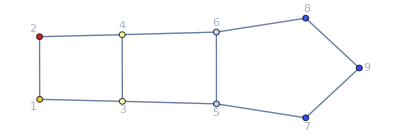

```mathematica
ColorNetworkByValueFunctionOperator[d2e][rule]
```

```mathematica
{timedata,d2e}=AbsoluteTiming[D2E[Data/.{I1-> 1,I2->2, U1-> 1,U2->2,U3->3}]];
timedata;
{time,{system,result}}=AbsoluteTiming@CriticalCongestionSolver[d2e];
time
```

1.4913

```mathematica
result=Solver[d2e][alpha=1];
```

The error (1-Norm of LHS-RHS) is 1.20737×10^-14

The error is 1.20737×10^-14 which is less than 1.×10^-10

It took 5.54414 seconds to solve!
	The system is True

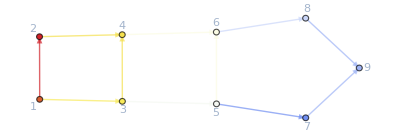

```mathematica
ColorNetworkByValueFunctionOperator[d2e][result]
```

```mathematica
d2e=D2E[Data/.{I1-> 2,I2->6, U1-> 1,U2->2,U3->0}];
{time,{system,rules}}=CriticalCongestionSolver[d2e]//AbsoluteTiming;
time
```

1.9647

```mathematica
{time,d2e}=AbsoluteTiming@D2E[Data/.{I1-> 2.00000000001515151515151515115151515115151515151551515151,I2->6, U1-> 3,U2->3,U3->0.}];
time
{time,{system,rules}}=CriticalCongestionSolver[d2e]//AbsoluteTiming;
time
```

0.102996

2.26777

#### Non-linear case

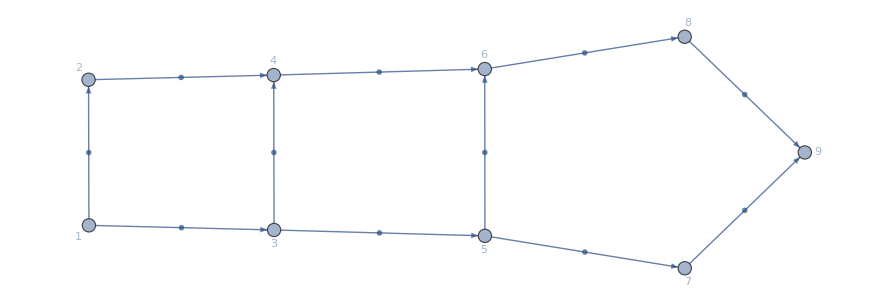

-Graphics-

```mathematica
(*Don't forget to change the Range!*)
alpha =1;
MFGEquations = d2e;
FFR=rules;
BEL=EdgeList[MFGEquations["BG"]];
pop=(#-> Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, (*PlotLabel->#,*)(*PlotRange->{-0.1,2.4},*)GridLines->Automatic,ImageSize->90])&/@BEL;
val=(#-> Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, (*PlotLabel->#,*)(*PlotRange->{-0.1,4.7},*)GridLines->Automatic,ImageSize->90])&/@BEL;
Graph[MFGEquations["BG"],EdgeLabels-> pop,GraphLayout->"SpringElectricalEmbedding"]
Graph[MFGEquations["BG"],EdgeLabels-> val,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
Solver[d2e][alpha = .1]
(*{timeFFR,FFR}= AbsoluteTiming[Catch@FixedPoint[FixedReduceX1[d2e1],rules1,200]//N//KeySort]*)
```

### The nonlinear solver solves the critical congestion case when the alpha is 1 and the initial currents are all zero.

```mathematica
rules0=AssociationThread[Values@d2e["jvars"],Table[0,{i,1,Length@d2e["jvars"]}]]
```

```mathematica
alpha = 1;
{timeFFR,FFR}= AbsoluteTiming@Catch@FixedPoint[FixedReduceX1[d2e],rules0, 1]
```

```mathematica
rules0=AssociationThread[Values @ d2e["jvars"],Table[0,{i,1,Length@d2e["jvars"]}]];
alpha = 1;
{timeFFR,FFR}= AbsoluteTiming@KeySort@Catch@FixedPoint[FixedReduceX1[d2e],rules0, 1]
d2e["EqCriticalCase"]/.FFR
```

### Test on a “large” network

#### D2E already takes half a minute. Set the option of giving the Graph with GridGraph, for example. Would this run faster?

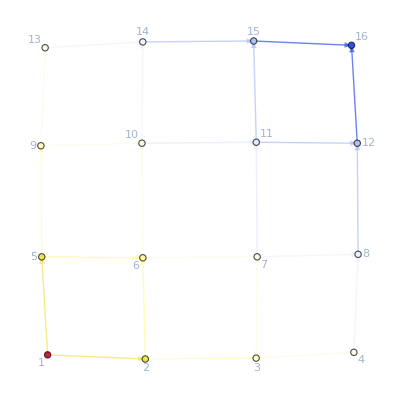

```mathematica
eme=4;
ege=4;
ete =1;
gr=GridGraph[{eme,ege,ete},DirectedEdges->True];
{timegridata,d2egrid}=AbsoluteTiming@D2E[
AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->4},(*FinalCosts=*){{eme*ege*ete,U1}/.U1->0},(*SwitchingCostsData=*){}}]
];
{timegrid,{systemgrid,rulesgrid}}=CriticalCongestionSolver[d2egrid]//AbsoluteTiming;
timegrid
systemgrid
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid]
```

```mathematica
systemgrid//Solve//FindInstance
```

FindInstance[{{jt28→ConditionalExpression[1/7 (6-7 jt31), 0≤jt31≤6/7],jt40→ConditionalExpression[1/7 (4-7 jt43), 0≤jt43≤4/7],jt64→ConditionalExpression[1/7 (6-7 jt67), 0≤jt67≤4/7],jt76→ConditionalExpression[1/7 (6-7 jt79), 0≤jt79≤6/7]}}]

```mathematica
Manipulate[eme=2;
ege=3;
ete =1;
gr=GridGraph[{eme,ege},DirectedEdges->True];
Datagrid =AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->400},(*FinalCosts=*){{eme*ege*ete,U1}/.U1->0, {eme*ege*ete-1,0}, {eme*ege*ete-2,U2}},(*SwitchingCostsData=*){}}];
{timegridata,d2egrid}=AbsoluteTiming@D2E[Datagrid];
{timegrid,{systemgrid,rulesgrid}}=CriticalCongestionSolver[d2egrid]//AbsoluteTiming;
Print[timegrid];
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid],{{U2,100},0,1000,10}]
```

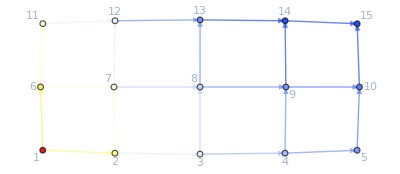

```mathematica
eme=5;
ege=3;
gr=GridGraph[{eme,ege},DirectedEdges->True];
Datagrid =AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->400},(*FinalCosts=*){{eme*ege,U1}/.U1->0, {eme*ege-1,0}, {eme*ege-2,U2}/.U2->100},(*SwitchingCostsData=*){}}];
{timegridata,d2egrid}=AbsoluteTiming@D2E[Datagrid];
{timegrid,{systemgrid,rulesgrid}}=CriticalCongestionSolver[d2egrid]//AbsoluteTiming;
Print["It took ",timegrid, " seconds to solve the critical congestion case."];
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid]
```

```mathematica
gr=GridGraph[{3,7},DirectedEdges->True, VertexLabels->"Name"];
Data =AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{8,I1}/.I1->400},(*FinalCosts=*){{17,U1}/.U1->0},(*SwitchingCostsData=*){}}];
```

```mathematica
gr=GridGraph[{3,3},DirectedEdges->True];
Data =AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->4,{3,4}},(*FinalCosts=*){{5,U1}/.U1->0(*,{8,0}*)},(*SwitchingCostsData=*){}}];
{timegridata,d2egrid}=AbsoluteTiming@D2E[Data];
alpha=1;
(rulesgrid = Solver[d2egrid][alpha]);
```

# TestZone

#### This is the winning code! Try this on CriticalCongestionSolverNewReduce

```mathematica
{system,rules}=((And@@(NewReduce/@(Select[system,Function[a,!FreeQ[a,#]]]&/@Values[d2egrid["uvars"]]))//Simplify)&&system)//CleanEqualities
```

# This is in the code already:

### Color representation of the value function (this is suitable for the critical congestion case because the value function is linear on each edge)

#### New function!!!

```mathematica
eStyle[colors_][pts_,DirectedEdge[x_,y_]]:={colors[[y]],Arrow[Line[pts,VertexColors->{colors[[x]],colors[[y]]}]]}

ColorNetworkByValueFunctionOperator[d2e1_Association][rules_]:= Module[{values,colors},
values=d2e1["VL"]/.KeyMap[#[[1]]&,d2e1["uvars"]/.rules];(*this works WITHOUT switching costs*)
(*Print[values];*)
colors=ColorData["TemperatureMap"]/@(values/Max[values]);
(*Print[colors];*)
GraphicsGrid[{
{HighlightGraph[SetProperty[d2e1["BG"],EdgeShapeFunction-> eStyle[colors]],Thread[Style[d2e1["VL"],colors]],GraphLayout->"SpringElectricalEmbedding"]},
{BarLegend["TemperatureMap",LegendMarkerSize->100,LegendLayout->"ReversedRow"]}
}]
]
```

### Idea:

```mathematica
eStyle[colors_][pts_,DirectedEdge[x_,y_]]:={colors[[y]],Arrow[Line[pts,VertexColors->{colors[[x]],colors[[y]]}]]}
g=GridGraph[{4,4},VertexLabels->"Name",ImagePadding->10,DirectedEdges->True];
colors=ColorData["TemperatureMap"]/@(VertexDegree[g]/Max[VertexDegree[g]]);
HighlightGraph[SetProperty[g,EdgeShapeFunction->eStyle[colors]],Thread[Style[VertexList[g],colors]]]
```